((32/T^2+(32 ⅇ^(8/T))/T^2) T)/(4 (12+2 ⅇ^(-8/T)+2 ⅇ^(8/T)))

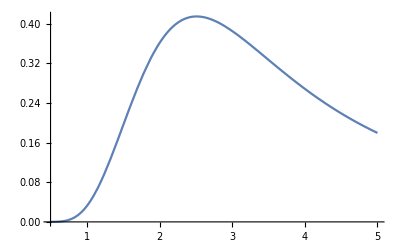

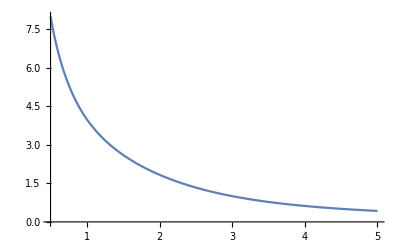

```mathematica
Clear["Global`*"]
Clear[Subscript]
Z=Exp[(8-4h)/T]+4Exp[-2h/T]+4Exp[0/T]+2Exp[-8/T]+4Exp[2h/T]+Exp[(8+4h)/T];
A=-T Log[Z];
Cvmol=-T D[A,{T,2}]/4/.h->0;
totSpin=T D[Log[Z],h];
chimol= D[totSpin,h]/4/.h->0
Plot[Cvmol,{T,0.5,5}]
Plot[chimol,{T,0.5,5}]
```

```mathematica
Table[Cvmol, {T,0.5,5,0.05}]
Table[chimol, {T,0.5,5,0.05}]
```

{0.0000432135,0.000152944,0.000431885,0.00102626,0.00213136,0.00397704,0.00680649,0.0108531,0.0163197,0.0233628,0.0320823,0.0425176,0.0546476,0.0683947,0.083632,0.100191,0.117872,0.13645,0.15569,0.175346,0.195179,0.214956,0.234457,0.253481,0.271847,0.289397,0.305999,0.321544,0.335946,0.349143,0.361096,0.371784,0.381203,0.389368,0.396304,0.402048,0.406649,0.410159,0.412638,0.414149,0.414759,0.414533,0.413539,0.411844,0.40951,0.406602,0.403179,0.399297,0.395012,0.390372,0.385426,0.380218,0.374787,0.369172,0.363406,0.357521,0.351544,0.345502,0.339417,0.33331,0.3272,0.321103,0.315033,0.309003,0.303024,0.297107,0.291259,0.285488,0.2798,0.2742,0.268693,0.263281,0.257967,0.252755,0.247644,0.242637,0.237733,0.232934,0.228239,0.223647,0.219159,0.214772,0.210486,0.2063,0.202212,0.198221,0.194325,0.190522,0.18681,0.183189,0.179655}

{8.,7.27271,6.66661,6.15371,5.71397,5.33271,4.99887,4.70396,4.44138,4.2059,3.9933,3.8002,3.62379,3.46179,3.31228,3.17367,3.04462,2.92402,2.81091,2.70448,2.60405,2.50904,2.41894,2.33334,2.25186,2.17419,2.10006,2.02921,1.96144,1.89657,1.83442,1.77486,1.71775,1.66296,1.61039,1.55993,1.51149,1.46497,1.42031,1.37741,1.3362,1.29661,1.25858,1.22204,1.18692,1.15317,1.12072,1.08954,1.05955,1.03072,1.00299,0.976315,0.950652,0.925957,0.90219,0.87931,0.85728,0.836062,0.815624,0.79593,0.77695,0.758652,0.741008,0.72399,0.707571,0.691725,0.676429,0.66166,0.647394,0.633611,0.620291,0.607414,0.594963,0.582919,0.571266,0.559988,0.54907,0.538497,0.528256,0.518332,0.508714,0.49939,0.490347,0.481575,0.473064,0.464803,0.456783,0.448995,0.44143,0.434079,0.426935}